```mathematica
(*Import T0,μ0 ;Export {T,μ,{possible M value}} *)
(*/////// This part is used to debug ///////*)
```

## Parameters

```mathematica
(*These parameters are caught from CI*)
mg=0.8;αir=0.93π;Λir=0.24;Λuv=0.905;
mu=0.007;
τir=1/Λir;τuv=1/Λuv;
(*T=0.0002*)
T=0.04;
(*μ from 0.01 to 0.5 ,0.01 every step*)
(*μstart=0;μend=0.5;μstep=0.01;
μ=Table[x,{x,start,end,step}];*)
μ=0.4;
(*M from 0.01 to 0.4 ,0.02 every step*)
Mstart=0;Mend=0.5;Mstep=0.1;
M=Table[x,{x,Mstart,Mend,Mstep}];
M0=Table[x,{x,Mstart,Mend,Mstep}];
(*the number of kernels*)
Kn=16;
```

## Function

```mathematica
(*This function is get from CI *)
Mass[M_,T_,μ_]:=mu+M*(16αir)/(3π*mg^2)*Ϛ[M,T,μ];
(*This function is similar to CI function C, also named Ϛ,but in different form*)
Ϛ[MIn_,Tin_,μin_]:=Module[
	{
	T=Tin,μ=μin,M=MIn,
	t,l0=-1,result=0,int1,int2,int3,value1,
	W,s0
	},(*Local variable*)
(*simplify the calculation*)
t=M^2-μ^2;
W[l_]:=(2*l+1)*π*T;
value1=1/4*NIntegrate[(E^(-τ*M^2))/τ^2 EllipticTheta[3,(π*T+I*μ)/(2T),E^(-1/(4*T^2*τ))],{τ,τuv^2,τir^2}];
If[t>=-π^2 T^2,
result=value1;
	];(*the result curve is good!*)
If[t<-π^2 T^2,
l0=1/2*(Sqrt[-t/(π^2 T^2)]-1);
(*(w_(l`))^2+t>=0*)
int1=value1-(T*Sqrt[π])/2*∑_(l1=Floor[-l0])^Floor[l0] NIntegrate[(E^(-τ*(M^2-μ^2+(W[l1])^2+2I*W[l1]*μ)))/τ^(3/2),{τ,τuv^2,τir^2}];
(*(w_(l`))^2+t<0*)
s0[l_]:=-t-(W[l])^2;

int2=T*∑_(l2=Floor[-l0])^Floor[l0] NIntegrate[E^(-τ*(M^2-μ^2+(W[l2])^2+2I*W[l2]*μ))*(2 E^(-τ*s0[l2])*√(s0[l2]*τ)+√π*Erfc[√(s0[l2]*τ)])/(2 τ^(3/2)),{τ,τuv^2,τir^2}];
(*Math*)
int3=T*∑_(l3=Floor[-l0])^Floor[l0] (s0[l3])^(3/2)*NIntegrate[E^(τ*(M^2-μ^2+(W[l3])^2+2I*W[l3]*μ))*ExpIntegralE[-1/2,-τ*s0[l3]],{τ,τuv^2,τir^2}];
(*correct function*)
int33=-T*∑_(l3=Floor[-l0])^Floor[l0] NIntegrate[E^(-τ*(t+(W[l3])^2+2I*W[l3]*μ))*(-2 E^(-τ*s0[l3])*√(s0[l3]*τ)+√π*Erf[√(s0[l3]*τ)])/(2 τ^(3/2)),{τ,τuv^2,τir^2}];
(*Nfunction wrong*)
int31=-T*∑_(l3=Floor[-l0])^Floor[l0] NIntegrate[s^(1/2)E^(-τ*(s+t+(W[l3])^2+2I*W[l3]*μ)),{τ,τuv^2,τir^2},{s,0,s0[l3]}];
result=int1+int2+int33;
];
result
]
```

## Calculate

```mathematica
(*Gobal variance*)
(*Code*)
CloseKernels[];
LaunchKernels[Kn];
SetSharedVariable[M];

ParallelDo[
M[[i]]=Mass[M0[[i]],T,μ];
,
{i,Length[M]}
];

Do[
Print[M[[i]]]
,{i,Length[M]}
]
```

0.007+0. ⅈ

0.0957579+8.06155×10^-18 ⅈ

0.198125+1.15606×10^-18 ⅈ

0.306931+7.93656×10^-19 ⅈ

0.373368+3.57554×10^-19 ⅈ

0.375001+1.12736×10^-19 ⅈ

## Draw Chart

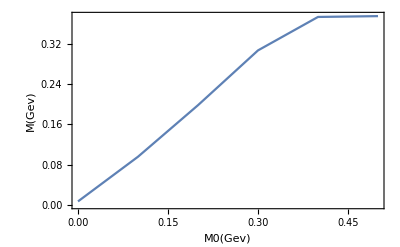

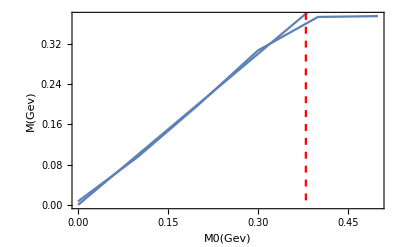

```mathematica
(*Gobal variance*)
chart;lin1;lin2;
(*Code*)
(*Draw chart, get real part of M*)
Do[
M[[i]]=Re[M[[i]]]
,{i,Length[M]}
]
(*Definite chart*)
chart=ListLinePlot[
Transpose[{M0,M}],
Frame->True,
FrameLabel->{Style["M0(Gev)",Bold,12.5],Style["M(Gev)",Bold,12.5]},
PlotRange->Full
]
(*The compare line:the left hand side of the formula*)
lin1=Plot[x,{x,0,0.5}];
(*Show*)
If[
Im[√(μ^2-π^2*T^2)]==0,
lin2=ContourPlot[x==√(μ^2-π^2*T^2),{x,0,M0[[Length[M0]]]},{y,0,M0[[Length[M0]]]},ContourStyle->{Red,Dashed}];(*bound line:red*)

Show[chart,lin1,lin2]
]
If[
Im[√(μ^2-π^2*T^2)]≠0,
Show[chart,lin1]
]
```

## Fix

```mathematica
(*Gobal variance*)
(*Function*)
Fix1[Mx_,My_,bound_]:=Module[
{
	y=My,t=Mx,b=bound,(*input table*)
	p,point,
model,p1,p2,p3,p4,p0,f(*parameters*)
	},(*Local variable*)
(*together in to a two-dimension table*)
p[i_]:={t[[i]],y[[i]]};
point=Table[N[p[i],10],{i,Floor[b]}];
model=p4*x^4+p3*x^3+p2*x^2+p1*x+p0;
f=FindFit[point,model,{p1,p2,p3,p4,p0},x];
model/.f
]
Fix2[Mx_,My_,bound_]:=Module[
{
	y=My,t=Mx,b=bound,(*input table*)
	p,point,
model,p1,p2,p3,f,p4,p0(*parameters*)
	},(*Local variable*)
(*together in to a two-dimension table*)
p[i_]:={t[[i]],y[[i]]};
point=Table[p[i],{i,Ceiling[b],Length[t]}];
model=p4*x^4+p3*x^3+p2*x^2+p1*x+p0;
f=FindFit[point,model,{p1,p2,p3,p4,p0},x];
model/.f
]
GetNnumber[a_,b_,c_,d_,n_]:=Module[
{
all,z,xp,zi,p0
},
all={a,b,c,d};
z=Flatten[all];
xp=Position[z,x];

zi=Delete[z,xp];
zi
]
(*Code*)
(*Create a two deminsion table*)
p[i_]:={M0[[i]],M[[i]]};
point=Table[p[i],{i,Length[M0]}];
(*Judge:we desprate M0 into two areas:bound line*)
ggbond=(Re[√(μ^2-π^2*T^2)]-Mstart)/Mstep+1;
If[ggbond<=1,ggbond=0.5;];
If[ggbond>=Length[M0],ggbond=Length[M0]+0.5;];
(*Condition one:the bound line is in the middle of the zone*)
If[ggbond>=1∧ggbond<=Length[M0],
function1=Fix1[M0,M,ggbond];
function2=Fix2[M0,M,ggbond]
(*plot1=Plot[function1,{x,0,M0[[Floor[ggbond]]]}];
plot2=Plot[function2,{x,M0[[Ceiling[ggbond]]],M0[[Length[M0]]]}];
chart2=ListPlot[point];;
Show[plot1,plot2,chart2,PlotRange->Full];*)
];
(*Condition two:the bound line is on the left side of the zone*)
If[ggbond==0.5,
function2=Fix2[M0,M,ggbond]
(*plot2=Plot[function2,{x,M0[[Ceiling[ggbond]]],M0[[Length[M0]]]}];
chart2=ListPlot[point];;
Show[plot2,chart2,PlotRange->Full];*)
];

(*Condition three:the bound line is on the right side of the zone*)
If[ggbond==Length[M0]+0.5,
function1=Fix1[M0,M,ggbond]
(*plot1=Plot[function1,{x,0,M0[[Floor[ggbond]]]}];
chart2=ListPlot[point];;
Show[plot1,chart2,PlotRange->Full];*)
];
```

## Get Point

```mathematica
(*Gobal variance*)
(*Code*)
Out1={{x}};Out2={{x}};Out3={{x}};Out4={{x}};Outt={};
(*Condition one:the bound line is in the middle of the zone*)
If[ggbond>=1∧ggbond<=Length[M0],
Out1=NSolve[{function1-x==0,0<=x<=M0[[Floor[ggbond]]]},x]/.Rule->List;
Out2=NSolve[{function2-x==0,M0[[Ceiling[ggbond]]]<=x<=M0[[Length[M0]]]},x]/.Rule->List;
]
(*Condition two:the bound line is on the left side of the zone*)
If[ggbond==0.5,
Out3=NSolve[{function2-x==0,M0[[Ceiling[ggbond]]]<=x<=M0[[Length[M0]]]},x]/.Rule->List;
]
(*Condition three:the bound line is on the right side of the zone*)
If[ggbond==Length[M0]+0.5,
Out4=NSolve[{function1-x==0,0<=x<=M0[[Floor[ggbond]]]},x]/.Rule->List;
]
Outt=GetNnumber[Out1,Out2,Out3,Out4,10];
Lire={T,μ,Outt}
```

{0.0005,0.38,{}}

{0.0005,0.35,{}}

{0.0005,0.4,{0.036569,0.294266}}

{0.0005,0.4,{0.036569,0.294266}}

{0.0005,0.4,{}}

{0.0005,0.4,{}}

{0.0005,0.4,{}}

«1 more identical outputs»

{0.0005,0.4,{0.036569,0.294266}}

{0.0005,0.4,{0.036569,0.294266}}

{0.0005,0.4,{0.036569,0.294266}}

«1 more identical outputs»

{0.0005,0.4,{0.007}}

{0.001,0.4,{}}

{0.001,0.4,{}}

{0.001,0.4,{}}

«3 more identical outputs»

{0.001,0.4,{0.0365685,0.294265}}

{0.005,0.4,{0.0365713,0.294274}}

{0.005,0.4,{0.0365713,0.294274}}

{0.01,0.4,{0.0367224,0.294139}}

{0.01,0.4,{0.0367224,0.294139}}

{0.05,0.4,{}}

{0.03,0.4,{0.0375505,0.298983}}

{0.04,0.4,{0.0450625,0.223647}}